```mathematica
19
```

## My 2HDM

### FeynRules Input

#### Be sure to quit the kernel before continuing Here we initialise FeynRules, set our directories, and load our *.fr model

```mathematica
$FeynRulesPath=SetDirectory["/Users/laramason/Downloads/feynrules-current"];
<<FeynRules`;
SetDirectory[$FeynRulesPath<>"/Models/2HDM/2HDM_add_vevs"];
FR$Parallelize = False;

LoadModel["2HDM_S.fr"];
FeynmanGauge = False;
(* LoadRestriction["Cabibbo.rst", "Massless.rst"]*)
(*WriteUFO[L2HDM, Output->"2HDM_UFO_Unitary"];*)
```

- FeynRules -

Version: 2.3.32 ( 12 March 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

R. Islam

M. Kumar

Model Version: 1.1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Next-to-Minimal 2-Higgs-Doublet Model loaded.

Now we check the validity of the model

```mathematica
CheckHermiticity[LN2HDM, FlavorExpand->True]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

GetFC::Head: Wrong Head in FC.

Symbol

$Aborted

```mathematica
LHiggs
```

1280+1/4 c_w g_1 g_w s_w H_pp2$3474 H_pp2$3475 RA[pp2$3474,1] RA[pp2$3475,1] Z_mu^2+1/4 ⅈ A0 c_β c_w g_1 g_w s_w H_pp2$3476 RA[pp2$3476,2] Z_mu^2+1/4 c_w g_1 g_w s_β s_w vev H_pp2$3476 RA[pp2$3476,2] Z_mu^2-1/4 ⅈ A0 c_β c_w g_1 g_w s_w H_pp2$3477 RA[pp2$3477,2] Z_mu^2+1/4 c_w g_1 g_w s_β s_w vev H_pp2$3477 RA[pp2$3477,2] Z_mu^2+1/4 c_w g_1 g_w s_w H_pp2$3476 H_pp2$3477 RA[pp2$3476,2] RA[pp2$3477,2] Z_mu^2-1/8 ⅈ A0 g_1^2 s_β s_w^2 H_pp2$3478 RA[pp2$3478,1] Z_mu^2+1/8 c_β g_1^2 s_w^2 vev H_pp2$3478 RA[pp2$3478,1] Z_mu^2+1/8 ⅈ A0 g_1^2 s_β s_w^2 H_pp2$3479 RA[pp2$3479,1] Z_mu^2+1/8 c_β g_1^2 s_w^2 vev H_pp2$3479 RA[pp2$3479,1] Z_mu^2+1/8 g_1^2 s_w^2 H_pp2$3478 H_pp2$3479 RA[pp2$3478,1] RA[pp2$3479,1] Z_mu^2+1/8 ⅈ A0 c_β g_1^2 s_w^2 H_pp2$3480 RA[pp2$3480,2] Z_mu^2+1/8 g_1^2 s_β s_w^2 vev H_pp2$3480 RA[pp2$3480,2] Z_mu^2-1/8 ⅈ A0 c_β g_1^2 s_w^2 H_pp2$3481 RA[pp2$3481,2] Z_mu^2+1/8 g_1^2 s_β s_w^2 vev H_pp2$3481 RA[pp2$3481,2] Z_mu^2+1/8 g_1^2 s_w^2 H_pp2$3480 H_pp2$3481 RA[pp2$3480,2] RA[pp2$3481,2] Z_mu^2
 |  |  |  |

```mathematica
CheckDiagonalMassTerms[L2HDM]
```

Neglecting all terms with more than 2 particles.

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -h1 h2 mu1 RA[1,1] RA[2,1]-1.5 c_β^2 h1 h2 λ_1 vev^2 RA[1,1] RA[2,1]-1/2 h1 h2 λ_3 s_β^2 vev^2 RA[1,1] RA[2,1]-1/2 h1 h2 λ_4 s_β^2 vev^2 RA[1,1] RA[2,1]-0.5 h1 h2 λ_5 s_β^2 vev^2 RA[1,1] RA[2,1]+h1 h2 mu3 RA[1,2] RA[2,1]-c_β h1 h2 λ_3 s_β vev^2 RA[1,2] RA[2,1]-c_β h1 h2 λ_4 s_β vev^2 RA[1,2] RA[2,1]-1. c_β h1 h2 λ_5 s_β vev^2 RA[1,2] RA[2,1]+h1 h2 mu3 RA[1,1] RA[2,2]-c_β h1 h2 λ_3 s_β vev^2 RA[1,1] RA[2,2]-c_β h1 h2 λ_4 s_β vev^2 RA[1,1] RA[2,2]-1. c_β h1 h2 λ_5 s_β vev^2 RA[1,1] RA[2,2]-h1 h2 mu2 RA[1,2] RA[2,2]-1/2 c_β^2 h1 h2 λ_3 vev^2 RA[1,2] RA[2,2]-1/2 c_β^2 h1 h2 λ_4 vev^2 RA[1,2] RA[2,2]-0.5 c_β^2 h1 h2 λ_5 vev^2 RA[1,2] RA[2,2]-1.5 h1 h2 λ_2 s_β^2 vev^2 RA[1,2] RA[2,2]

False

```mathematica
CheckMassSpectrum[L2HDM]
```

Neglecting all terms with more than 2 particles.

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -(V^CKM)_(3,3)^* (y^d)_(3,3)^* (b^-)_(r$20439,cc).t_(r$20440,cc) cosb^† HP^† (P_-)_(r$20439,r$20440)+(V^CKM)_(3,3)^* (b^-)_(sp2$20433,cc).t_(sp2$20431,cc) HCanti[cosb] HCanti[HP] (P_+)_(sp2$20433,sp2$20431) (y^u)_(3,3)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -(V^CKM)_(2,1)^* (y^d)_(1,1)^* (d^-)_(r$20439,cc).c_(r$20440,cc) cosb^† HP^† (P_-)_(r$20439,r$20440)+(V^CKM)_(2,1)^* (d^-)_(sp2$20433,cc).c_(sp2$20431,cc) HCanti[cosb] HCanti[HP] (P_+)_(sp2$20433,sp2$20431) (y^u)_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -(V^CKM)_(1,1)^* (y^d)_(1,1)^* (d^-)_(r$20439,cc).u_(r$20440,cc) cosb^† HP^† (P_-)_(r$20439,r$20440)+(V^CKM)_(1,1)^* (d^-)_(sp2$20433,cc).u_(sp2$20431,cc) HCanti[cosb] HCanti[HP] (P_+)_(sp2$20433,sp2$20431) (y^u)_(1,1)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -(V^CKM)_(2,2)^* (y^d)_(2,2)^* (s^-)_(r$20439,cc).c_(r$20440,cc) cosb^† HP^† (P_-)_(r$20439,r$20440)+(V^CKM)_(2,2)^* (s^-)_(sp2$20433,cc).c_(sp2$20431,cc) HCanti[cosb] HCanti[HP] (P_+)_(sp2$20433,sp2$20431) (y^u)_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -(V^CKM)_(1,2)^* (y^d)_(2,2)^* (s^-)_(r$20439,cc).u_(r$20440,cc) cosb^† HP^† (P_-)_(r$20439,r$20440)+(V^CKM)_(1,2)^* (s^-)_(sp2$20433,cc).u_(sp2$20431,cc) HCanti[cosb] HCanti[HP] (P_+)_(sp2$20433,sp2$20431) (y^u)_(1,1)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (y^l)_(1,1)^* (e^-)_r$20453.ve_r$20454 HP^† sinb^† (P_-)_(r$20453,r$20454)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (y^l)_(2,2)^* (mu^-)_r$20453.vm_r$20454 HP^† sinb^† (P_-)_(r$20453,r$20454)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (y^l)_(3,3)^* (ta^-)_r$20453.vt_r$20454 HP^† sinb^† (P_-)_(r$20453,r$20454)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (V^CKM)_(2,1) (y^u)_(2,2)^* (c^-)_(r$20463,cc).d_(r$20464,cc) HCanti[cosb]^† HCanti[HP]^† (P_-)_(r$20463,r$20464)-cosb HP (V^CKM)_(2,1) (c^-)_(sp2$20436,cc).d_(sp2$20430,cc) (P_+)_(sp2$20436,sp2$20430) (y^d)_(1,1)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (V^CKM)_(2,2) (y^u)_(2,2)^* (c^-)_(r$20463,cc).s_(r$20464,cc) HCanti[cosb]^† HCanti[HP]^† (P_-)_(r$20463,r$20464)-cosb HP (V^CKM)_(2,2) (c^-)_(sp2$20436,cc).s_(sp2$20430,cc) (P_+)_(sp2$20436,sp2$20430) (y^d)_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (V^CKM)_(3,3) (y^u)_(3,3)^* (t^-)_(r$20463,cc).b_(r$20464,cc) HCanti[cosb]^† HCanti[HP]^† (P_-)_(r$20463,r$20464)-cosb HP (V^CKM)_(3,3) (t^-)_(sp2$20436,cc).b_(sp2$20430,cc) (P_+)_(sp2$20436,sp2$20430) (y^d)_(3,3)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (V^CKM)_(1,1) (y^u)_(1,1)^* (u^-)_(r$20463,cc).d_(r$20464,cc) HCanti[cosb]^† HCanti[HP]^† (P_-)_(r$20463,r$20464)-cosb HP (V^CKM)_(1,1) (u^-)_(sp2$20436,cc).d_(sp2$20430,cc) (P_+)_(sp2$20436,sp2$20430) (y^d)_(1,1)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: (V^CKM)_(1,2) (y^u)_(1,1)^* (u^-)_(r$20463,cc).s_(r$20464,cc) HCanti[cosb]^† HCanti[HP]^† (P_-)_(r$20463,r$20464)-cosb HP (V^CKM)_(1,2) (u^-)_(sp2$20436,cc).s_(sp2$20430,cc) (P_+)_(sp2$20436,sp2$20430) (y^d)_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: 1/2 ⅈ A0 c_β h1 HP λ_4 sinb HCanti[cosb] HCanti[HP] R_α_(1,1)-(0.+0.5 ⅈ) A0 c_β h1 HP λ_5 sinb HCanti[cosb] HCanti[HP] R_α_(1,1)-1/2 ⅈ A0 c_β cosb h1 HP λ_4 HCanti[HP] HCanti[sinb] R_α_(1,1)+(0.+0.5 ⅈ) A0 c_β cosb h1 HP λ_5 HCanti[HP] HCanti[sinb] R_α_(1,1)+1/2 ⅈ A0 h1 HP λ_4 s_β sinb HCanti[cosb] HCanti[HP] R_α_(1,2)-(0.+0.5 ⅈ) A0 h1 HP λ_5 s_β sinb HCanti[cosb] HCanti[HP] R_α_(1,2)-1/2 ⅈ A0 cosb h1 HP λ_4 s_β HCanti[HP] HCanti[sinb] R_α_(1,2)+(0.+0.5 ⅈ) A0 cosb h1 HP λ_5 s_β HCanti[HP] HCanti[sinb] R_α_(1,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: 1/2 ⅈ A0 c_β h2 HP λ_4 sinb HCanti[cosb] HCanti[HP] R_α_(2,1)-(0.+0.5 ⅈ) A0 c_β h2 HP λ_5 sinb HCanti[cosb] HCanti[HP] R_α_(2,1)-1/2 ⅈ A0 c_β cosb h2 HP λ_4 HCanti[HP] HCanti[sinb] R_α_(2,1)+(0.+0.5 ⅈ) A0 c_β cosb h2 HP λ_5 HCanti[HP] HCanti[sinb] R_α_(2,1)+1/2 ⅈ A0 h2 HP λ_4 s_β sinb HCanti[cosb] HCanti[HP] R_α_(2,2)-(0.+0.5 ⅈ) A0 h2 HP λ_5 s_β sinb HCanti[cosb] HCanti[HP] R_α_(2,2)-1/2 ⅈ A0 cosb h2 HP λ_4 s_β HCanti[HP] HCanti[sinb] R_α_(2,2)+(0.+0.5 ⅈ) A0 cosb h2 HP λ_5 s_β HCanti[HP] HCanti[sinb] R_α_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -h1 h2 mu1 R_α_(1,1) R_α_(2,1)-1.5 c_β^2 h1 h2 λ_1 vev^2 R_α_(1,1) R_α_(2,1)-1/2 h1 h2 λ_3 s_β^2 vev^2 R_α_(1,1) R_α_(2,1)-1/2 h1 h2 λ_4 s_β^2 vev^2 R_α_(1,1) R_α_(2,1)-0.5 h1 h2 λ_5 s_β^2 vev^2 R_α_(1,1) R_α_(2,1)-cosb h1 h2 HP λ_3 HCanti[cosb] HCanti[HP] R_α_(1,1) R_α_(2,1)-1. h1 h2 HP λ_1 sinb HCanti[HP] HCanti[sinb] R_α_(1,1) R_α_(2,1)+h1 h2 mu3 R_α_(1,2) R_α_(2,1)-c_β h1 h2 λ_3 s_β vev^2 R_α_(1,2) R_α_(2,1)-c_β h1 h2 λ_4 s_β vev^2 R_α_(1,2) R_α_(2,1)-1. c_β h1 h2 λ_5 s_β vev^2 R_α_(1,2) R_α_(2,1)+1/2 h1 h2 HP λ_4 sinb HCanti[cosb] HCanti[HP] R_α_(1,2) R_α_(2,1)+0.5 h1 h2 HP λ_5 sinb HCanti[cosb] HCanti[HP] R_α_(1,2) R_α_(2,1)+1/2 cosb h1 h2 HP λ_4 HCanti[HP] HCanti[sinb] R_α_(1,2) R_α_(2,1)+0.5 cosb h1 h2 HP λ_5 HCanti[HP] HCanti[sinb] R_α_(1,2) R_α_(2,1)+h1 h2 mu3 R_α_(1,1) R_α_(2,2)-c_β h1 h2 λ_3 s_β vev^2 R_α_(1,1) R_α_(2,2)-c_β h1 h2 λ_4 s_β vev^2 R_α_(1,1) R_α_(2,2)-1. c_β h1 h2 λ_5 s_β vev^2 R_α_(1,1) R_α_(2,2)+1/2 h1 h2 HP λ_4 sinb HCanti[cosb] HCanti[HP] R_α_(1,1) R_α_(2,2)+0.5 h1 h2 HP λ_5 sinb HCanti[cosb] HCanti[HP] R_α_(1,1) R_α_(2,2)+1/2 cosb h1 h2 HP λ_4 HCanti[HP] HCanti[sinb] R_α_(1,1) R_α_(2,2)+0.5 cosb h1 h2 HP λ_5 HCanti[HP] HCanti[sinb] R_α_(1,1) R_α_(2,2)-h1 h2 mu2 R_α_(1,2) R_α_(2,2)-1/2 c_β^2 h1 h2 λ_3 vev^2 R_α_(1,2) R_α_(2,2)-1/2 c_β^2 h1 h2 λ_4 vev^2 R_α_(1,2) R_α_(2,2)-0.5 c_β^2 h1 h2 λ_5 vev^2 R_α_(1,2) R_α_(2,2)-1.5 h1 h2 λ_2 s_β^2 vev^2 R_α_(1,2) R_α_(2,2)-1. cosb h1 h2 HP λ_2 HCanti[cosb] HCanti[HP] R_α_(1,2) R_α_(2,2)-h1 h2 HP λ_3 sinb HCanti[HP] HCanti[sinb] R_α_(1,2) R_α_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: 1/2 c_w g_1 g_w s_β vev A_mu HCanti[cosb] HCanti[HP] W_mu-1/2 c_β c_w g_1 g_w vev A_mu HCanti[HP] HCanti[sinb] W_mu

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: 1/2 cosb c_w g_1 g_w HP s_β vev A_mu W_mu^†-1/2 c_β c_w g_1 g_w HP sinb vev A_mu W_mu^†

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: HP sinb (ve^-)_sp2$20427.e_sp2$20425 (P_+)_(sp2$20427,sp2$20425) (y^l)_(1,1)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: HP sinb (vm^-)_sp2$20427.mu_sp2$20425 (P_+)_(sp2$20427,sp2$20425) (y^l)_(2,2)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: HP sinb (vt^-)_sp2$20427.ta_sp2$20425 (P_+)_(sp2$20427,sp2$20425) (y^l)_(3,3)

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -1/4 c_β^2 c_w^2 g_1 g_w vev^2 A_mu Z_mu-1/4 c_w^2 g_1 g_w s_β^2 vev^2 A_mu Z_mu-1/4 c_β^2 c_w g_1^2 s_w vev^2 A_mu Z_mu+1/4 c_β^2 c_w g_w^2 s_w vev^2 A_mu Z_mu-1/4 c_w g_1^2 s_β^2 s_w vev^2 A_mu Z_mu+1/4 c_w g_w^2 s_β^2 s_w vev^2 A_mu Z_mu+1/4 c_β^2 g_1 g_w s_w^2 vev^2 A_mu Z_mu+1/4 g_1 g_w s_β^2 s_w^2 vev^2 A_mu Z_mu+1/2 cosb c_w^2 g_1 g_w HP A_mu HCanti[cosb] HCanti[HP] Z_mu-1/2 cosb c_w g_1^2 HP s_w A_mu HCanti[cosb] HCanti[HP] Z_mu+1/2 cosb c_w g_w^2 HP s_w A_mu HCanti[cosb] HCanti[HP] Z_mu-1/2 cosb g_1 g_w HP s_w^2 A_mu HCanti[cosb] HCanti[HP] Z_mu+1/2 c_w^2 g_1 g_w HP sinb A_mu HCanti[HP] HCanti[sinb] Z_mu-1/2 c_w g_1^2 HP sinb s_w A_mu HCanti[HP] HCanti[sinb] Z_mu+1/2 c_w g_w^2 HP sinb s_w A_mu HCanti[HP] HCanti[sinb] Z_mu-1/2 g_1 g_w HP sinb s_w^2 A_mu HCanti[HP] HCanti[sinb] Z_mu

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -1/2 g_1 g_w s_β s_w vev HCanti[cosb] HCanti[HP] W_mu Z_mu+1/2 c_β g_1 g_w s_w vev HCanti[HP] HCanti[sinb] W_mu Z_mu

Warning: not numerical value encountered. Unable to decide whether mass term is diagonal

Non diagonal mass term found: -1/2 cosb g_1 g_w HP s_β s_w vev W_mu^† Z_mu+1/2 c_β g_1 g_w HP sinb s_w vev W_mu^† Z_mu

```mathematica
CheckDiagonalKineticTerms[L2HDM]
```

All kinetic terms are diagonal.

True

```mathematica
CheckKineticTermNormalisation[L2HDM, FlavorExpand->True]
```

Neglecting all terms with more than 2 particles.

All kinetic terms are diagonal.

Warning: Kinetic term for {ve, vebar} seems not to be correctly normalized.

Warning: Kinetic term for {vm, vmbar} seems not to be correctly normalized.

Warning: Kinetic term for {vt, vtbar} seems not to be correctly normalized.

#### Generate FeynRules Output UFO

```mathematica
WriteUFO[L2HDM, Output->"2HDM_UFO_Unitary"];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

88 possible non-zero vertices have been found -> starting the computation:  / 88.

84 vertices obtained.

Flavor expansion of the vertices:  / 84

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 110

Squared matrix elent compute in 3.6332 seconds.

Decay widths computed in 0.062988 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

- Optimizing: /162 .

- Writing files.

Done!

#### Generate Feynman Rules

```mathematica
(*verts2HDM = FeynmanRules[L2HDM]*)
(*verts2HDM = FlavourExpansion[ verts2HDM ]*)
vertsG=SelectVertices[verts2HDM,SelectParticles->{{G,G,G},{G,G,G,G}}]
(*decays = ComputeWidths[ verts2HDM ] *)
```

Applying seclection rules...

{{{{G,1},{G,2},{G,3}},g_s f_(a_1,a_2,a_3) p_1^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_2^μ_3 η_(μ_1,μ_2)-g_s f_(a_1,a_2,a_3) p_1^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_3^μ_2 η_(μ_1,μ_3)+g_s f_(a_1,a_2,a_3) p_2^μ_1 η_(μ_2,μ_3)-g_s f_(a_1,a_2,a_3) p_3^μ_1 η_(μ_2,μ_3)},{{{G,1},{G,2},{G,3},{G,4}},ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_4) η_(μ_2,μ_3)+ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_2,Gluon$1) f_(a_3,a_4,Gluon$1) η_(μ_1,μ_3) η_(μ_2,μ_4)-ⅈ g_s^2 f_(a_1,a_4,Gluon$1) f_(a_2,a_3,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)-ⅈ g_s^2 f_(a_1,a_3,Gluon$1) f_(a_2,a_4,Gluon$1) η_(μ_1,μ_2) η_(μ_3,μ_4)}}

Now we generate the input for FeynArts

```mathematica
WriteFeynArtsOutput[L2HDM, FlavorExpand->SU2W]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: 2HDM_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

88 possible non-zero vertices have been found -> starting the computation:  / 88.

84 vertices obtained.

Writing FeynArts model file into directory 2HDM_FA

Writing FeynArts generic file on 2HDM_FA.gen.

Initialise FeynArts, FormCalc

Be sure to quit the Kernel before continuing

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"2HDM_FA","2HDM_FA"}];
(*_Hel=0;*)
```

FeynArts 3.10 (21 Jan 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

Check that the model files exist

```mathematica
FileExistsQ[model<>".mod"]
FileExistsQ[model<>".gen"]
```

True

True

Create Topologies

> Top. 1 ad/bdcd/0.m, 1 diagram

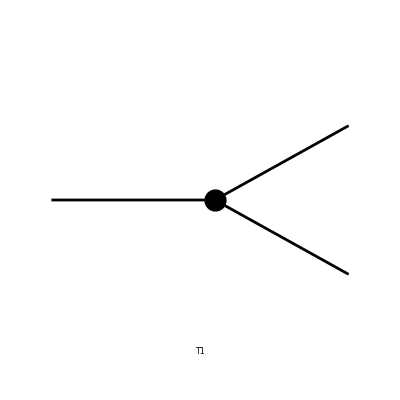

```mathematica
topo=CreateTopologies[0,1->2];
Paint[topo];
```

Insert some fields: let’s start with inserting a scalar (H)

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

TopologyList[Process→{S[2]}→{V[1],V[1]},Model→{/Users/laramason/Downloads/feynrules-current/Models/2HDM_add_vevs/2HDM_FA/2HDM_FA},GenericModel→{/Users/laramason/Downloads/feynrules-current/Models/2HDM_add_vevs/2HDM_FA/2HDM_FA},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][4],Field[1]],Propagator[Outgoing][Vertex[1][2],Vertex[3][4],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][4],Field[3]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[2],Field[2]→V[1],Field[3]→V[1]]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[2],Field[2]→V[1],Field[3]→V[1]]]]]

> Top. 1 ad/bdcd/0.m, 1 diagram

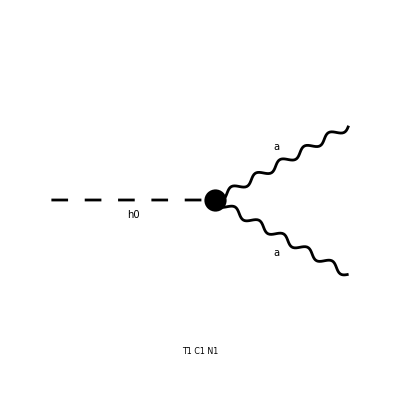

```mathematica
diag=InsertFields[topo,{S[2]}->{V[1],V[1]},InsertionLevel->{Classes},
Model->model,GenericModel->model]
Paint[diag];
```

Calculate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA]
SquaredME[amp]
%[[1]]//.%[[2]]
%//FullForm
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 3 Classes amplitudes

> Top. 3: 3 Classes amplitudes

in total: 7 Classes amplitudes

preparing FORM code in /Users/laramason/fc-amp-1.frm

running FORM...

ReadForm::formerror: \!\(\*RowBox[{"\"MH has been declared as a symbol \\nIllegal use of function arguments\\nInternal error in code generator.\""}]\)

$Aborted

SquaredME[amp,amp]

ReplaceRepeated::reps: \!\(\*RowBox[{"{", "amp", "}"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

amp//.amp

ReplaceRepeated[amp,amp]